(Wmax (-Erf[(√π (x-h Cot[θ]-ai (1+Cot[θ] Tan[α])))/r]+Erf[(√π (x-h Cot[θ]-ais1 (1+Cot[θ] Tan[α])))/r]))/(2 (1+Cot[θ] Tan[α]))

1/2 Wmax (Erf[(√π y)/r]-Erf[(√π (-L1+y))/r])

((-ⅇ^(-(π (-ai+x-h Cot[θ]-ai Cot[θ] Tan[α])^2)/r^2)+ⅇ^(-(π (-ais1+x-h Cot[θ]-ais1 Cot[θ] Tan[α])^2)/r^2)) Wmax)/(r (1+Cot[θ] Tan[α]))

((ⅇ^(-(π y^2)/r^2)-ⅇ^(-(π (-L1+y)^2)/r^2)) Wmax)/r

(b2 (-ⅇ^(-(π (-ai+x-Cot[θ] (h+ai Tan[α]))^2)/r^2)+ⅇ^(-(π (-ais1+x-Cot[θ] (h+ais1 Tan[α]))^2)/r^2)) Wmax)/(1+Cot[θ] Tan[α])-(Wmax Cot[θ] (-Erf[(√π (x-h Cot[θ]-ai (1+Cot[θ] Tan[α])))/r]+Erf[(√π (x-h Cot[θ]-ais1 (1+Cot[θ] Tan[α])))/r]))/(2 (1+Cot[θ] Tan[α]))

b1 (-ⅇ^(-(π y^2)/r^2)+ⅇ^(-(π (-L1+y)^2)/r^2)) Wmax

8500

900

550

172

0

8500

900

1473

112

0

8500

900

718

109

0

8500

900

239

116

0

8500

900

1042

109

0

8500

900

919

160.3

0

8500

900

635.4

94

0

8500

900

434

86

0

8500

900

193.4

88

0

2300

345

146.6

71

0

-408.25 (-Erf[0.0085797 (-21.+x)]+Erf[0.0085797 (-20.79+x)]) (-Erf[0.0085797 (-96.6+y)]+Erf[0.0085797 y])

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

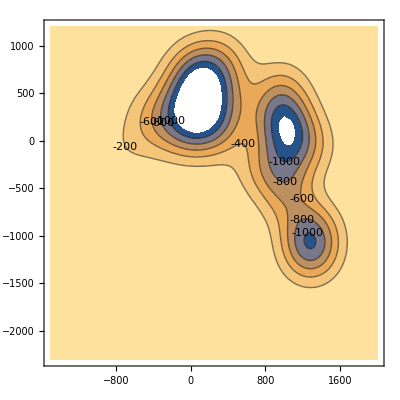

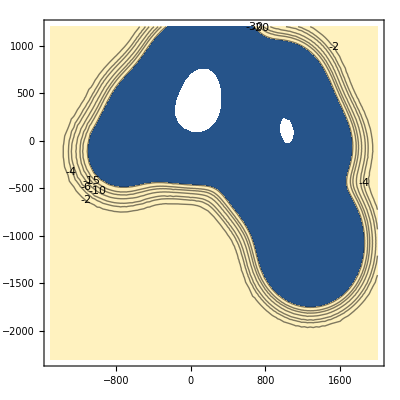

-Graphics3D-

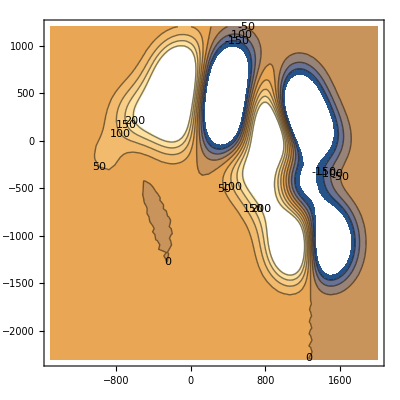

-Graphics3D-

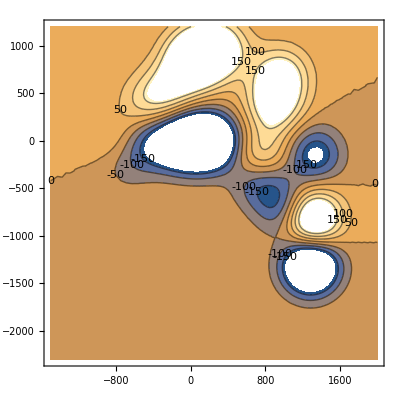

-Graphics3D-

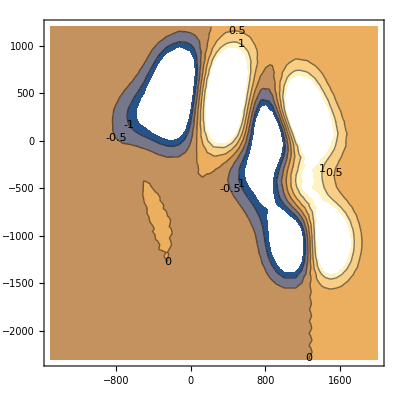

-Graphics3D-

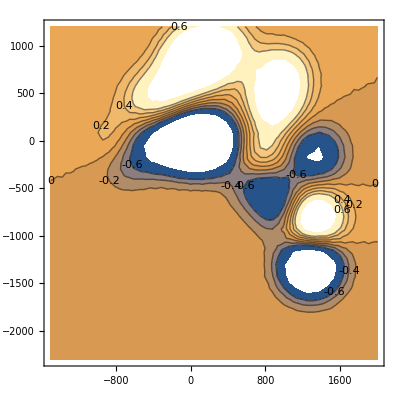

-Graphics3D-

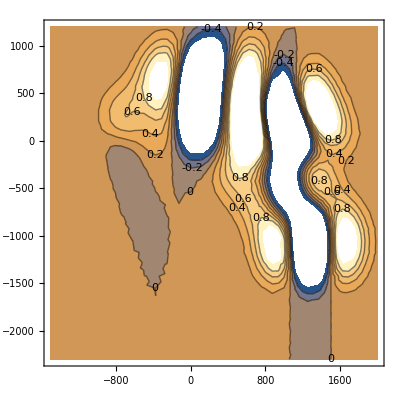

-Graphics3D-

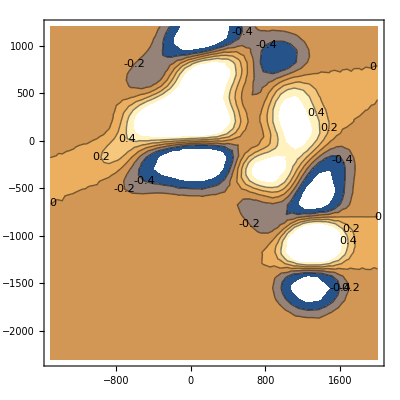

-Graphics3D-

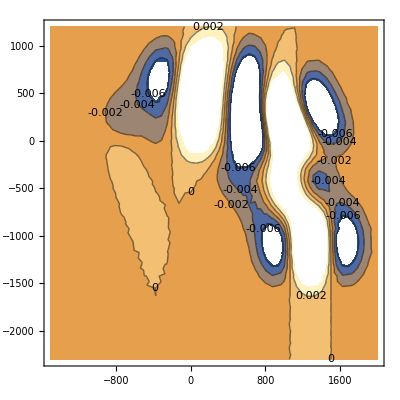

-Graphics3D-

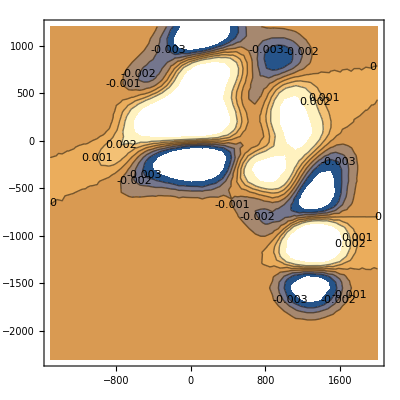

-Graphics3D-

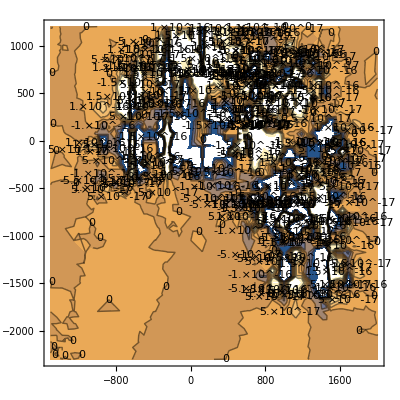

-Graphics3D-

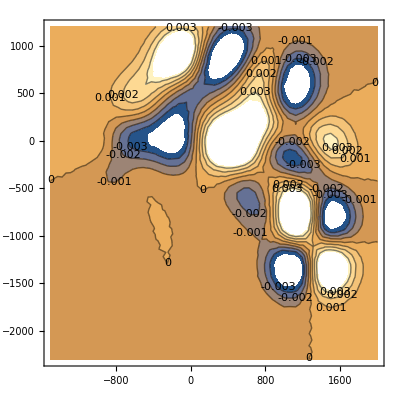

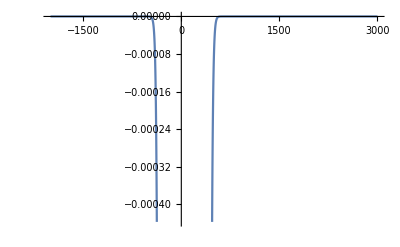

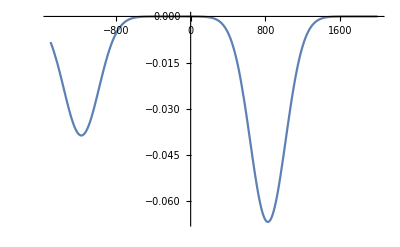

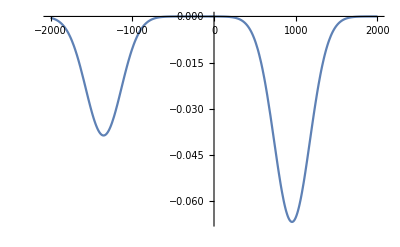

-Graphics3D-

-Graphics3D-

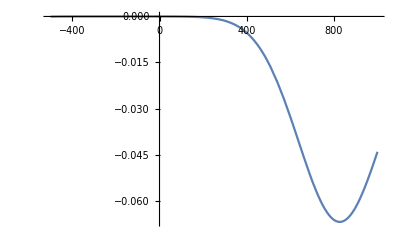

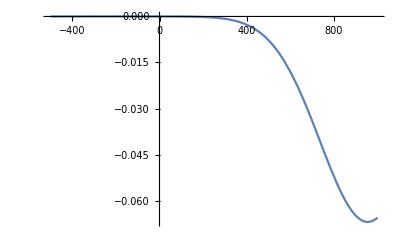

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(*通用模块0*)
(*注意方向*)
(*单一倾斜工作面*)
W0[x]=Wmax/(2 (1+Cot[θ] Tan[α])) (Erf[(√π (x-h*Cot[θ]-ais1 (1+Cot[θ] Tan[α])))/r]-Erf[(√π (x-h*Cot[θ]-ai (1+Cot[θ] Tan[α])))/r])(*倾向*)
W0[y]=1/2 Wmax (Erf[(√π y)/r]-Erf[(√π (y-L1))/r])(*走向*)
W0dx[x]=Wmax/(r* (1+Cot[θ] Tan[α]))(ⅇ^(-(π (x-ais1-h*Cot[θ]-ais1 Cot[θ] Tan[α])^2)/(r)^2)-ⅇ^(-(π (x-ai-h*Cot[θ]-ai Cot[θ] Tan[α])^2)/(r)^2))(*倾向*)
W0dy[y]=Wmax/r(ⅇ^(-(π y^2)/(r)^2) -ⅇ^(-(π (y-L1)^2)/(r)^2) ) 
U0[x]=(b2 * Wmax)/(1+Cot[θ] Tan[α])(ⅇ^(-(π (x-ais1-Cot[θ] (h+ais1 Tan[α]))^2)/(r)^2)-ⅇ^(-(π (x-ai-Cot[θ] (h+ai Tan[α]))^2)/(r)^2))-Cot[θ]*W0[x]
U0[y]=b1 *Wmax*(ⅇ^(-(π (y-L1)^2)/(r)^2)-ⅇ^(-(π y^2)/(r)^2)) 
(*注意
W0[y]=Wmax/(2 (1+Cot[θ] Tan[α])) (Erf[(√π (y-h*Cot[θ]-ais1 (1+Cot[θ] Tan[α])))/r]-Erf[(√π (y-h*Cot[θ]-ai (1+Cot[θ] Tan[α])))/r])
W0[x]=1/2 Wmax (Erf[(√π x)/r]-Erf[(√π (x-L1))/r])
W0dx[x]=Wmax/r(ⅇ^(-(π x^2)/(r)^2) -ⅇ^(-(π (x-L1)^2)/(r)^2) ) 
W0dy[y]=Wmax/(r* (1+Cot[θ] Tan[α]))(ⅇ^(-(π (y-ais1-h*Cot[θ]-ais1 Cot[θ] Tan[α])^2)/(r)^2)-ⅇ^(-(π (y-ai-h*Cot[θ]-ai Cot[θ] Tan[α])^2)/(r)^2))
U0[x]=b1 *Wmax*(ⅇ^(-(π (x-L1)^2)/(r)^2)-ⅇ^(-(π x^2)/(r)^2)) 
U0[y]=(b2 * Wmax)/(1+Cot[θ] Tan[α])(ⅇ^(-(π (y-ais1-Cot[θ] (h+ais1 Tan[α]))^2)/(r)^2)-ⅇ^(-(π (y-ai-Cot[θ] (h+ai Tan[α]))^2)/(r)^2))-Cot[θ]*W0[y]
方向*)

(*---循环函数:小条分累加---*)
FXY:=For[n=100;i=1;Wxy=0;Wxyi=0;Uxy=0;Uxyi=0;Vxy=0;Vxyi=0,i<=n,i=i+1,
ais1=((i-1)/n)*L2*Cos[α];
ai=((i)/n)*L2*Cos[α];
hi=h+(2i-1)/2n*L2*Sin[α];
r=hi/tanb;

W0yi=W0[y];
W0xi=W0[x];
Wxyi=-1/Wmax*W0yi*W0xi;
Wxy=Wxy+Wxyi;
U0xi=U0[x];
U0yi=U0[y];
Uxyi=1/Wmax*U0xi*W0yi;
Uxy=Uxy+Uxyi;
Vxyi=1/Wmax*U0yi*W0xi;
Vxy=Vxy+Vxyi
];
(**)
(*二次运算函数：求解其他变形*)
(**)
GXY:=Module[{},

Tx=D[Wxy,x];
Ty=D[Wxy,y];

Ex=D[Uxy,x];
Ey=D[Vxy,y];
Exy=D[Uxy,y]+D[Vxy,x];

Kx=D[Tx,x];
Ky=D[Ty,y];
Kxy=D[Wxy,x,y];
]
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(*通用模块2：地表移动基本参数*)
CXY:=Module[{},
yita=0.71;
tanb=1.67;
b=0.3;
(*gdj=0.02;s1=gdj*H1*)
s1=25;

(*中间量计算-循环输入量*)
θ=Pi/2-0.5*α;
Wmax=m1*yita;
L2=L2c1-2*s1;
L1=L1c1-2*s1;
h=H1;
b1=b;
b2=b;
]
(**)
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(**)
(*相似模块1：坐标系旋转*)
(*如下为模式匹配规则1：*)
(*
(*坐标系旋转*)(*及*-单工作面结果输出记录保存--*)
RXY0:=Module[{},
ψ=-38/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=1088;
yO=-1214;
x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;
Wxyt1=Wxy;
Uxyt1=Uxy;
Vxyt1=Vxy;
Txt1=Tx;
Tyt1=Ty;
Ext1=Ex;
Eyt1=Ey;
Kxt1=Kx;
Kyt1=Ky;
]
*)
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(*开始累积工作面-------------------------------------------------------------------------------------------------------------------------*)
(**)
(*----------------------------01工作面3209----------------------------------------*)
(*3209采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=550(*m*)
L2c1=172(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY1:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=1222.54;
yO=-1320.89;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt1=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt1=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt1=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt1=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt1=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext1=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt1=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt1=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt1=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt1=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt1=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY1
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------02工作面3201----------------------------------------*)
(*3201采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=1473(*m*)
L2c1=112(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY2:=Module[{},
ψ=3/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=966;
yO=-791;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt2=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt2=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt2=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt2=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt2=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext2=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt2=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt2=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt2=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt2=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt2=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY2
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------03工作面3107----------------------------------------*)
(*3107采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=718(*m*)
L2c1=109(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY3:=Module[{},
ψ=41/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=876.9;
yO=-983.2;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt3=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt3=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt3=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt3=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt3=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext3=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt3=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt3=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt3=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt3=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt3=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY3
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------04工作面3200----------------------------------------*)
(*3200采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=239(*m*)
L2c1=116(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY4:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=710;
yO=-394;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt4=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt4=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt4=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt4=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt4=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext4=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt4=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt4=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt4=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt4=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt4=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY4
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------05工作面3106----------------------------------------*)
(*3106采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=1042(*m*)
L2c1=109(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY5:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=290.4;
yO=-12.9;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt5=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt5=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt5=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt5=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt5=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext5=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt5=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt5=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt5=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt5=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt5=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY5
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------06工作面3105----------------------------------------*)
(*3105采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=919(*m*)
L2c1=160.3(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY6:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=0;
yO=0;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt6=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt6=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt6=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt6=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt6=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext6=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt6=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt6=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt6=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt6=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt6=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY6
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------07工作面3103----------------------------------------*)
(*3103采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=635.4(*m*)
L2c1=94(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY7:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=-224.6;
yO=-30.1;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt7=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt7=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt7=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt7=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt7=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext7=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt7=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt7=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt7=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt7=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt7=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY7
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------08工作面3001----------------------------------------*)
(*3001采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=434(*m*)
L2c1=86(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY8:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=-480;
yO=4.0;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt8=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt8=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt8=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt8=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt8=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext8=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt8=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt8=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt8=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt8=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt8=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY8
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)
(*----------------------------09工作面3002----------------------------------------*)
(*3002采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=8500
H1=900(*m*)
L1c1=193.4(*m*)
L2c1=88(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXY9:=Module[{},
ψ=21/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=-764.3;
yO=79.2;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxyt9=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxyt9=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxyt9=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txt9=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tyt9=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Ext9=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eyt9=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxt9=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kyt9=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Exyt9=Exy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxyt9=Kxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXY9
(**)
(*----------------------------单工作面end----------------------------------------*)
(**)

(*----------------------------0t工作面E3105----------------------------------------*)
(*E3112采空区参数*)(*L1、b1为走向参数;L2、b2为倾向参数*)
m1=2300
H1=345(*m*)
L1c1=146.6(*m*)
L2c1=71(*m*)

α=0/180*Pi
(*---------1反演得到的随机介质基本参数---------*)
(*---------中间量计算-循环输入量----------------*)
CXY
(*---2循环函数:小条分累加---*)
FXY
(*3二次运算函数：求解其他变形*)
GXY
(*4单工作面结果输出记录保存*-及*-坐标系旋转--*)
RXYt:=Module[{},
ψ=0/180*Pi;
(*XO、YO为子坐标系在母坐标系中坐标*)
xO=0;
yO=0;
(*x=xt*Cos[ψ]+yt*Sin[ψ]-xO;
y=-xt*Sin[ψ]+yt*Cos[ψ]-yO;*)
Wxytt=Wxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Uxytt=Uxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Vxytt=Vxy/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Txtt=Tx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Tytt=Ty/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Extt=Ex/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Eytt=Ey/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kxtt=Kx/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
Kytt=Ky/.{x->(xt*Cos[ψ]+yt*Sin[ψ]-xO),y->(-xt*Sin[ψ]+yt*Cos[ψ]-yO)};
]
(**)
RXYt
(**)
(*----------------------------单工作面end----------------------------------------*)

(*结束-累积工作面-------------------------------------------------------------------------------------------------------------------------*)
(*----t0测试：单次结果记录---*)
Wxyi
Wxy;
(*单次结果绘图-局部坐标系*)
Plot3D[Wxyi,{x,50,500},{y,-100,500}]
Plot3D[Wxy,{x,-100,300},{y,-100,500}]
Plot3D[Kx,{x,-100,300},{y,-100,500}]
(**)

(**)
(*--------总绘图变量-----------*)
WxyA=Wxyt1+Wxyt2+Wxyt3+Wxyt4+Wxyt5+Wxyt6+Wxyt7+Wxyt8+Wxyt9;
UxA=Uxyt1+Uxyt2+Uxyt3+Uxyt4+Uxyt5+Uxyt6+Uxyt7+Uxyt8+Uxyt9;
UyA=Vxyt1+Vxyt2+Vxyt3+Vxyt4+Vxyt5+Vxyt6+Vxyt7+Vxyt8+Vxyt9;
TxA=Txt1+Txt2+Txt3+Txt4+Txt5+Txt6+Txt7+Txt8+Txt9;
TyA=Tyt1+Tyt2+Tyt3+Tyt4+Tyt5+Tyt6+Tyt7+Tyt8+Tyt9;
ExA=Ext1+Ext2+Ext3+Ext4+Ext5+Ext6+Ext7+Ext8+Ext9;
EyA=Eyt1+Eyt2+Eyt3+Eyt4+Eyt5+Eyt6+Eyt7+Eyt8+Eyt9;
KxA=Kxt1+Kxt2+Kxt3+Kxt4+Kxt5+Kxt6+Kxt7+Kxt8+Kxt9;
KyA=Kyt1+Kyt2+Kyt3+Kyt4+Kyt5+Kyt6+Kyt7+Kyt8+Kyt9;

ExyA=Exyt1+Exyt2+Exyt3+Exyt4+Exyt5+Exyt6+Exyt7+Exyt8+Exyt9;
KxyA=Kxyt1+Kxyt2+Kxyt3+Kxyt4+Kxyt5+Kxyt6+Kxyt7+Kxyt8+Kxyt9;
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(*---整体绘图模块---*)

Plot3D[WxyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[WxyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]
ContourPlot[WxyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All,Contours->{-2,-4,-6,-10,-15,-20,-30}]

Plot3D[UxA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[UxA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[UyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[UyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[TxA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[TxA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[TyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[TyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[ExA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[ExA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[EyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[EyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KxA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KxA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[ExyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[ExyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KxyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KxyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

(*-----------------------------------------------------*)
(*--------------------------------------------------------------------------------------------------------------------------------------------*)
(*------------------曲线绘图模块-------------------*)
(*-----局部坐标系------*)
Wtx=Wxy/.{x->0.5*L2c1};
Plot[Wtx,{y,-2000,3000}]
Wtx2=WxyA/.{yt->(-Tan[Pi/6]*(xt-19)-1569)};
Plot[Wtx2,{xt,-1500,2000}]
Wtx3=Wtx2/.{xt->xl*Cos[Pi/6]};
Plot[Wtx3,{xl,-2000,2000}]
(*----------------------------------------------------*)
(*------------------绘图验证模块-------------------*)
Plot3D[Wxytt,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
Plot3D[Wxytt,{xt,-300,300},{yt,-500,500},PlotRange->Full]
(*----------------------------------------------------*)
nWtx2t1=WxyA/.{yt->(-0.577*(xt-19)-1569)};
Plot[nWtx2t1,{xt,-500,1000}]
nWtx3t1=nWtx2t1/.{xt->xl*0.866};
Plot[nWtx3t1,{xl,-500,1000}]
```

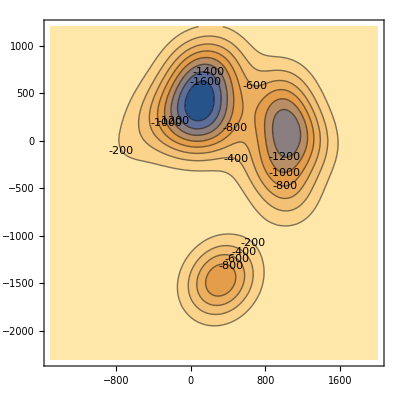

W0

```mathematica
ContourPlot[WxyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]
```

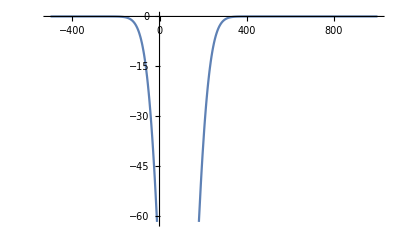

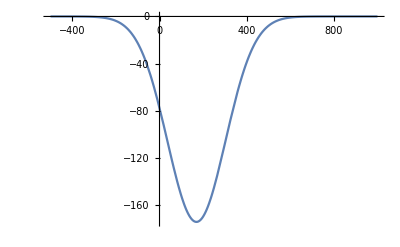

```mathematica
Wtx2=WxyA/.{yt->(-Tan[60/180*Pi]*(xt-19)-1569)};
Plot[Wtx2,{xt,-500,1000}]
Wtx3=Wtx2/.{xt->xl*Cos[60/180*Pi]};
Plot[Wtx3,{xl,-500,1000}]
```

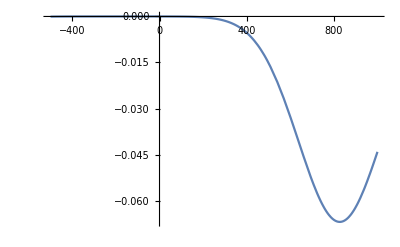

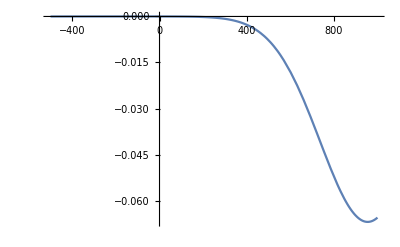

```mathematica
nWtx2t1=WxyA/.{yt->(-0.577*(xt-19)-1569)};
Plot[nWtx2t1,{xt,-500,1000}]
nWtx3t1=nWtx2t1/.{xt->xl*0.866};
Plot[nWtx3t1,{xl,-500,1000}]
```

```mathematica
-Tan[6/Pi]*(xt-19)-1569
```

-1569-(-19+xt) Tan[6/π]

```mathematica
LWxyt1=Wxyt2+Wxyt4
Plot3D[LWxyt1,{xt,-1500,3000},{yt,-2300,3000},PlotRange->Full]
Plot3D[LWxyt1,{xt,-300,300},{yt,-500,500},PlotRange->Full]
```

1
 |  |  |  |

-Graphics3D-

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
ContourPlot[ExA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[EyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[EyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KxA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KxA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[ExyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[ExyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]

Plot3D[KxyA,{xt,-1500,2000},{yt,-2300,1200},PlotRange->Full]
ContourPlot[KxyA,{xt,-1500,2000},{yt,-2300,1200},ContourLabels->All]
```

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-